```mathematica
Integrate[-9/16(t^3-t^2-t/9+1/9),{t,-1,1}]
```

1/4

```mathematica
Integrate[-27/16(t^3+t^2/3-t-1/3),{t,-1,1}]
```

3/4

```mathematica
(1.1539-1.5576)/(1.1-0.5)
```

-0.672833

```mathematica
(0.56448-1.1539)/(2.53-1.1)
```

-0.412182

```mathematica
(-0.41218+0.67283)/(2.53-0.5)
```

0.128399

```mathematica
(0.46914-0.56448)/(2.9-2.53)
```

-0.257676

```mathematica
(-0.257676+0.41218)/(2.9-1.1)
```

0.0858356

```mathematica
(0.0858356-0.128399)/(2.9-0.5)
```

-0.0177348

```mathematica
f[x_]:=1.55760-0.67283(x-0.5)+0.128399(x-0.5)(x-1.1)-0.0177348(x-0.5)(x-1.1)(x-2.53)
```

```mathematica
f[2]
```

0.734383

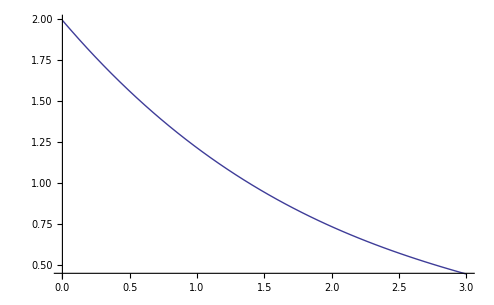

```mathematica
Plot[f[x],{x,0,3}]
```

```mathematica
(0.27067-0.46914)/(4-2.9)
```

-0.180427

```mathematica
(0.09957-0.27067)/(6-4)
```

-0.08555

```mathematica
(-0.08555+0.180427)/(6-2.9)
```

0.0306055

```mathematica
(-0.180427+0.257676)/(4-2.53)
```

0.0525503

```mathematica
InterpolatingPolynomial[{{0.5,1.55760},{1.1,1.15390},{2.53,0.56448},{2.9,0.46914}},x]
```

0.46914+(-0.453525+(0.121838-0.0177346 (-1.1+x)) (-0.5+x)) (-2.9+x)

```mathematica
%//Expand
```

1.98931-0.959817 x+0.201644 x^2-0.0177346 x^3

```mathematica
0.46914*(-2.9)
```

-1.36051

```mathematica
(0.0306055-0.0525503)/(6-2.53)
```

-0.00632415

```mathematica
(0.0525503-0.0858356)/(4-1.1)
```

-0.0114777

```mathematica
(0.0858356-0.128399)/(2.9-0.5)
```

-0.0177348

```mathematica
(-0.00632415+0.0114777)/(6-1.1)
```

0.00105174

```mathematica
(-0.0114777+0.0177348)/(4-0.5)
```

0.00178774

```mathematica
(0.00105174-0.00178774)/(6-0.5)
```

-0.000133818

```mathematica
g[x_]:=1.55760-0.67283(x-0.5)+0.128399(x-0.5)(x-1.1)-0.0177348(x-0.5)(x-1.1)(x-2.53)-0.00632415(x-0.5)(x-1.1)(x-2.53)(x-2.9)-0.000133818(x-0.5)(x-1.1)(x-2.53)(x-2.9)(x-4)
```

```mathematica
g[2]
```

0.730483

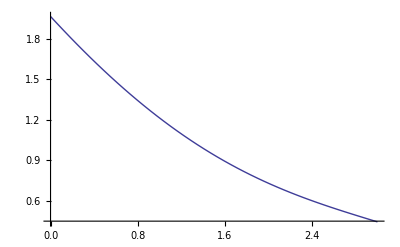

```mathematica
Plot[g[x],{x,0,3}]
```

```mathematica
?Solve
```

Solve[expr,vars] attempts to solve the system expr of equations or inequalities for the variables vars. 
Solve[expr,vars,dom] solves over the domain dom. Common choices of dom are Reals, Integers, and Complexes.

```mathematica
NSolve[{a*Exp[b*0.5]==1.55760,a*Exp[b*1.1]==1.15390,a*Exp[b*2.53]==0.56448,a*Exp[b*2.9]==0.46914},{a,b},Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

```mathematica
NSolve[{a*Exp[b*0.5]==1.55760,a*Exp[b*1.1]==1.15390},{a,b},Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→2.,b→-0.499998}}

```mathematica
2*Exp[0.5*(-0.5)]
```

1.5576

```mathematica
2*Exp[2.53*(-0.5)]
```

0.564479

```mathematica
f[x_]:=2*Exp[-0.5*x]
```

```mathematica
f''''[x]
```

0.125 ⅇ^(-0.5 x)

```mathematica
f'[x]
```

-1. ⅇ^(-0.5 x)

```mathematica
0.125*ⅇ^(-0.5*1)*(1/24)*(2-0.5)(2-1.1)(2-2.53)(2-2.9)
```

0.00203425

```mathematica
(x-Cos[1/(2(2+1))π])(x-Cos[3/(2(2+1))π])(x-Cos[5/(2(2+1))π])
```

x (-(√3)/2+x) ((√3)/2+x)

```mathematica
h[x_]:=x (-(√3)/2+x) ((√3)/2+x)
```

```mathematica
h[2]
```

2 (2-(√3)/2) (2+(√3)/2)

```mathematica
%//N
```

6.5

```mathematica
?ChebyshevT
```

ChebyshevT[n,x] gives the Chebyshev polynomial of the first kind T_n(x).

```mathematica
ChebyshevT[3,2]/2^2
```

13/2

```mathematica
%//N
```

6.5

```mathematica
Cos[3*ArcCos[2]]
```

Cos[3 ArcCos[2]]

```mathematica
%//N
```

26.+0. ⅈ

```mathematica
∏_(k=0)^n (x-Cos[(2k+1)/(2(n+1))π])
```

∏_(k=0)^n (x-Cos[((1+2 k) π)/(2 (1+n))])

```mathematica
∏_(k=0)^n (x-Cos[(2k+1)/(2(n+1))π])==ChebyshevT[n+1,x]/2^n
```

∏_(k=0)^n (x-Cos[((1+2 k) π)/(2 (1+n))])==2^-n ChebyshevT[1+n,x]

```mathematica
Exp[-1]//N
```

0.367879

```mathematica
Exp[1]//N
```

2.71828

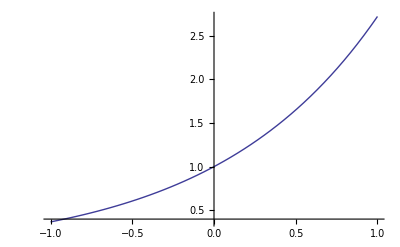

```mathematica
Plot[Exp[x],{x,-1,1}]
```

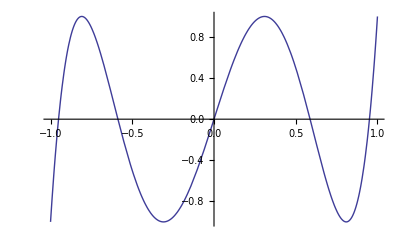

```mathematica
Plot[ChebyshevT[5,x],{x,-1,1}]
```

```mathematica
ⅇ/(2^4*5!)
```

ⅇ/1920

```mathematica
%//N
```

0.00141577

```mathematica
5!
```

120

```mathematica
?Interpolation
```

Interpolation[{f_1,f_2,…}] constructs an interpolation of the function values f_i, assumed to correspond to x values 1, 2, … . 
Interpolation[{{x_1,f_1},{x_2,f_2},…}] constructs an interpolation of the function values f_i corresponding to x values x_i.
Interpolation[{{{x_1,y_1,…},f_1},{{x_2,y_2,…},f_2},…}] constructs an interpolation of multidimensional data.
Interpolation[{{{x_1,…},f_1,df_1,…},…}] constructs an interpolation that reproduces derivatives as well as function values.
Interpolation[data,x] find an interpolation of data at the point x.

```mathematica
InterpolatingPolynomial[{{Cos[1/(2(4+1))π],0},{Cos[3/(2(4+1))π],0},{Cos[5/(2(4+1))π],0},{Cos[7/(2(4+1))π],0}},x]
```

0

```mathematica
Table[Exp[Cos[(2k+1)/(2(4+1))π]],{k,0,4}]
```

{ⅇ^(√(5/8+(√5)/8)),ⅇ^(√(5/8-(√5)/8)),1,ⅇ^(-√(5/8-(√5)/8)),ⅇ^(-√(5/8+(√5)/8))}

```mathematica
%//N
```

{2.58844,1.8,1.,0.555556,0.386333}

```mathematica
Table[Cos[(2k+1)/(2(4+1))π],{k,0,4}]//N
```

{0.951057,0.587785,0.,-0.587785,-0.951057}

```mathematica
(1.8-2.58844)/(0.587785-0.951054)
```

2.1704

```mathematica
(1-1.8)/(0-0.587785)
```

1.36104

```mathematica
(1.36104-2.1704)/(0-0.951057)
```

0.851011

```mathematica
(0.55556-1)/(-0.587785-0)
```

0.756127

```mathematica
(0.756127-1.36104)/(-0.587785-0.587785)
```

0.51457

```mathematica
(0.38633-0.55556)/(-0.951057+0.587785)
```

0.465849

```mathematica
(0.465849-0.756127)/(-0.951057-0)
```

0.305216

```mathematica
(0.51457-0.851011)/(-0.587785-0.951057)
```

0.218633

```mathematica
(0.305216-0.51457)/(-0.951057-0.587785)
```

0.136046

```mathematica
(0.136046-0.218633)/(-0.951057-0.951057)
```

0.0434185

```mathematica
p4[x_]:=2.58844+2.1704(x-0.951057)+0.851011(x-0.951057)(x-0.587785)+0.218633(x-0.951057)(x-0.587785)x+0.0434185(x-0.951057)(x-0.587785)x(x+0.587785)
```

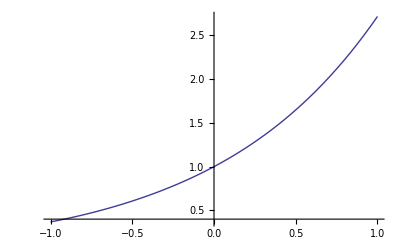

```mathematica
Plot[p4[x],{x,-1,1}]
```

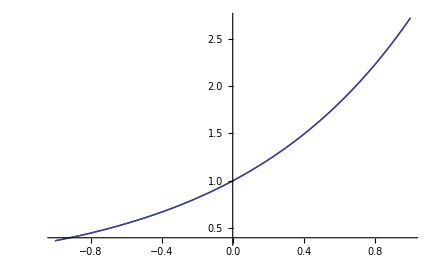

```mathematica
Show[Plot[p4[x],{x,-1,1}],Plot[Exp[x],{x,-1,1}]]
```

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

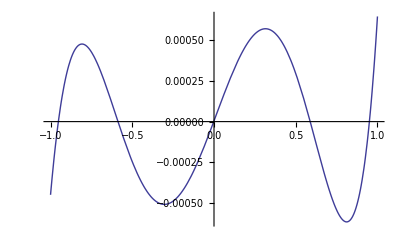

```mathematica
Plot[Exp[x]-p4[x],{x,-1,1}]
```

```mathematica
InterpolatingPolynomial[{{0,-1},{1,5/6},{2,1}},x]
```

-1+(11/6-5/6 (-1+x)) x

```mathematica
%//Expand
```

-1+(8 x)/3-(5 x^2)/6

```mathematica
Clear[p]
```

```mathematica
p[x_]:=-1+(8 x)/3-(5 x^2)/6
```

```mathematica
p'[0]
```

8/3

```mathematica
?InterpolatingPolynomial
```

InterpolatingPolynomial[{f_1,f_2,…},x] constructs an interpolating polynomial in x which reproduces the function values f_i at successive integer values 1,2,… of x. 
InterpolatingPolynomial[{{x_1,f_1},{x_2,f_2},…},x] constructs an interpolating polynomial for the function values f_i corresponding to x values x_i.
InterpolatingPolynomial[{{{x_1,y_1,…},f_1},{{x_2,y_2,…},f_2},…},{x,y,…}] constructs a multidimensional interpolating polynomial in the variables x,y,….
InterpolatingPolynomial[{{{x_1,…},f_1,df_1,…},…},{x,…}] constructs an interpolating polynomial that reproduces derivatives as well as function values.

```mathematica
p'[1]
```

1

```mathematica
Clear[p]
```

```mathematica
p[x_]:=a+b x+c x^2+d x^3+e x^4+f x^5
```

```mathematica
Solve[{p[0]==-1,p'[0]==2,p[1]==5/6,p'[1]==3/2,p[2]==1,p'[2]==-1},{a,b,c,d,e,f}]
```

{{a→-1,b→2,c→-2/3,d→17/12,e→-7/6,f→1/4}}

```mathematica
165
```

165

```mathematica
16*5
```

80

```mathematica
Clear[p]
```

```mathematica
p[x_]:=-1+2x-x 2/3+x^3 17/12-x^4 7/6+x^5 1/4
```

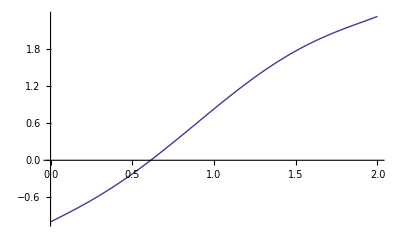

```mathematica
Plot[p[x],{x,0,2}]
```

```mathematica
Integrate[1/x,{x,1,2}]
```

Log[2]

```mathematica
%//N
```

0.693147

```mathematica
1/2/2
```

1/4

```mathematica
(1/2)/2
```

1/4

```mathematica
NSolve[Log[2]-1/m(3/4+∑_(v=1)^(m-1) 1/(1+v/m))<10^-5,m,Reals]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Log[2]-(3/4+m PolyGamma[0,2 m]-m PolyGamma[0,1+m])/m<1/100000,m,Reals]

```mathematica
Table[Log[2]-1/m(3/4+∑_(v=1)^(m-1) 1/(1+v/m)),{m,20,50}]//N
```

{-0.000156201,-0.000141683,-0.000129099,-0.00011812,-0.000108483,-0.00009998,-0.0000924385,-0.0000857192,-0.0000797067,-0.0000743053,-0.0000694348,-0.000065028,-0.0000610277,-0.0000573855,-0.0000540599,-0.0000510152,-0.0000482207,-0.0000456496,-0.0000432788,-0.000041088,-0.0000390594,-0.0000371775,-0.0000354283,-0.0000337998,-0.000032281,-0.0000308623,-0.0000295351,-0.0000282917,-0.0000271253,-0.0000260295,-0.0000249988}

```mathematica
10^-5
```

1/100000

```mathematica
%//N
```

0.00001

```mathematica
Clear[m,n,p,v]
```

```mathematica
Limit[∑_(v=1)^(m-1) (1+m/v),m->30]
```

11478499755427/77636318760

```mathematica
%//N
```

(10. (1.+v))/v

```mathematica
?Limit
```

Limit[expr,x->x_0] finds the limiting value of expr when x approaches x_0.

```mathematica
10^-5-Log[2]
```

1/100000-Log[2]

```mathematica
%//N
```

-0.693137

```mathematica
NSolve[∑_(v=1)^(m-1) (1+m/v)>10^-5-Log[2]+3/(4m),m,Reals]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-1+m+m HarmonicNumber[-1+m]>1/100000+3/(4 m)-Log[2],m,Reals]

```mathematica
Simplify[1/((1+(v-1)h+1+v h)/2)]
```

2/(2+h (-1+2 v))

```mathematica
%//FullSimplify
```

2/(2+h (-1+2 v))

```mathematica
NSolve[Log[2]-1/(3m)(3/4+2∑_(v=1)^m (2/(2+(2v-1)/m))+∑_(v=1)^(m-1) (1+m/v))<10^-5,m]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Log[2]-1/(3 m)(-1/4+m+m HarmonicNumber[-1+m]+2 (-m PolyGamma[0,1/2+m]+m PolyGamma[0,1/2+2 m]))<1/100000,m]

```mathematica
Table[Log[2]-1/(3m)(3/4+2∑_(v=1)^m (2/(2+(2v-1)/m))+∑_(v=1)^(m-1) (1+m/v)),{m,1,10}]//N
```

{-0.00129726,-0.388996,-0.572245,-0.691277,-0.779236,-0.848931,-0.906623,-0.955829,-0.998721,-1.03673}

```mathematica
f[x_]:=1/x
```

```mathematica
f''[x]
```

2/x^3

```mathematica
FindMaximum[f''[x],{x,1,2}]
```

FindMaximum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{1.11977×10^22,{x→5.63163×10^-8}}

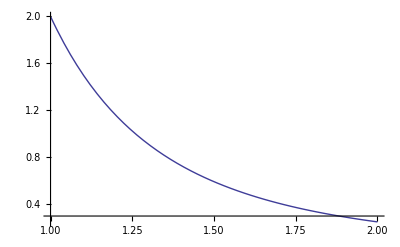

```mathematica
Plot[f''[x],{x,1,2}]
```

```mathematica
10^-5*6
```

3/50000

```mathematica
%//N
```

0.00006

```mathematica
Sqrt[%]
```

0.00774597

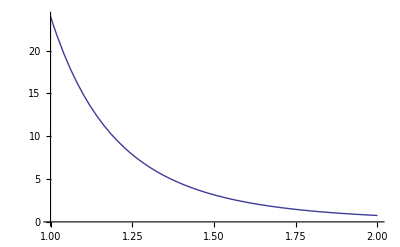

```mathematica
Plot[f''''[x],{x,1,2}]
```

```mathematica
f''''[1]
```

24

```mathematica
24/2880
```

1/120

```mathematica
10^-5*120
```

3/2500

```mathematica
Solve[h^4==3/2500,h,Reals]
```

```mathematica
{{h->-3^(1/4)/(5 √2)},{h->3^(1/4)/(5 √2)}}//N
```

{{h→-0.186121},{h→0.186121}}

```mathematica
1/2^5
```

1/32

```mathematica
32*80
```

2560

```mathematica
32*90
```

2880

```mathematica
1/3^5
```

```mathematica
1/243*3/80
```

```mathematica
1/6480*24
```

1/270

```mathematica
10^-5*90/24
```

3/80000

```mathematica
%//N
```

0.0000375

```mathematica
Solve[h^5==0.0000375,h,Reals]
```

{{h→0.130259}}

```mathematica
10^-5*6
```

3/50000

```mathematica
%//N
```

0.00006

```mathematica
10^-5*90/24
```

3/80000

```mathematica
Solve[h^3==0.00006,h,Reals]
```

{{h→0.0391487}}

```mathematica
Solve[h^5==3/80000,h,Reals]
```

{{h→3^(1/5)/(2 2^(2/5) 5^(4/5))}}

```mathematica
%//N
```

{{h→0.130259}}

```mathematica
10^-5*80/24
```

1/30000

```mathematica
Solve[h^5==1/30000,h,Reals]
```

{{h→1/(3^(1/5) 10^(4/5))}}

```mathematica
%//N
```

{{h→0.127226}}

```mathematica
1/0.039148676411688635
```

25.5436

```mathematica
1/26(∑_(v=1)^26 (1/(1+(2v-1)/2*(1/26))))
```

33273020379546955890144424732919464/48006022109803463870792829500460525

```mathematica
%//N
```

0.693101

```mathematica
Log[2]//N
```

0.693147

```mathematica
Integrate[1/x,{x,1,2}]
```

Log[2]

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n. 
D[f,x,y,…] differentiates f successively with respect to x,y,….
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives a tensor derivative.

```mathematica
Table[D[Log[x],{x,n}],{n,1,5}]
```

{1/x,-1/x^2,2/x^3,-6/x^4,24/x^5}

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

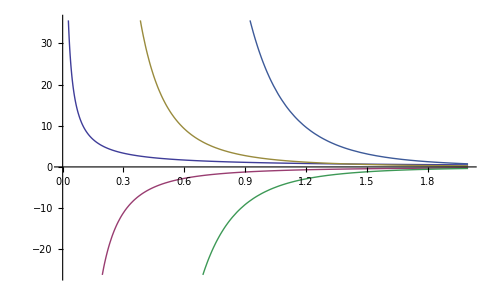

```mathematica
Plot[{1/x,-1/x^2,2/x^3,-6/x^4,24/x^5},{x,0,2}]
```

```mathematica
Integrate[x^(-1/2),{x,0,1}]
```

2

```mathematica
Integrate[2(t-1/2)(t-1)t^(-1/2),{t,0,1}]
```

4/5

```mathematica
Integrate[-4t(t-1)t^(-1/2),{t,0,1}]
```

16/15

```mathematica
Integrate[(t-1/2)2t t^(-1/2),{t,0,1}]
```

2/15

```mathematica
Integrate[x^(-1/2)*Exp[Sqrt[x]],{x,0,1}]
```

```mathematica
2 (-1+ⅇ)//N
```

3.43656

```mathematica
Integrate[t^(-1/2),t]
```

2 √t

```mathematica
D[Exp[Sqrt[x]],x]
```

ⅇ^(√x)/(2 √x)

```mathematica
Integrate[Exp[Sqrt[x]],x]
```

2 ⅇ^(√x) (-1+√x)

```mathematica
2/15(6+8Exp[Sqrt[1/2]]+Exp[1])
```

2/15 (6+ⅇ+8 ⅇ^(1/(√2)))

```mathematica
%//N
```

```mathematica
3.43656365691809-3.3257602242185094
```

0.110803